# Tesis de Sara v2.0

## Inicialización

```mathematica
Needs["AdvancedMapping`"];
```

## Caracterización de la estabilidad de los autómatas celulares

```mathematica
StillOrPeriodicQ[a1_,a2_,a3_]:=Or[SameQ[a1,a2],SameQ[a1,a3],SameQ[a2,a3]];
TestStillnessOrPeriodicity[rule_,maxIterations_]:=Block[{initialConfiguration,ca},
initialConfiguration = RandomInteger[1,{100,100}];
ca = NestWhileList[CellularAutomaton[<|"TotalisticCode"->rule,"Dimension"->2|>,#]&,initialConfiguration,!StillOrPeriodicQ[##]&,3,maxIterations];
If[Length[ca]==maxIterations+1,
Return[False],
Return[True]
];
];
TestStability[rule_,maxIterations_,repeats_]:=Block[{results},
results = Table[TestStillnessOrPeriodicity[rule,maxIterations],repeats];
If[Apply[And,results],
Return["Stable"],
If[!Apply[And,results]&& Apply[Or,results],
Return["Mixed"],
Return["Unstable"]
];
];
];
```

Primero caracterizamos los autómatas celulares según si son capaces de tener estados estables (no nos interesan las reglas que nunca llegan a un estado de estabilidad)

```mathematica
results = ProgressTable[{r,TestStability[r,1000,5]},{r,0,255}];
```

```mathematica
decoratedResults = ReplaceAll[results,{"Unstable"->Style["Unstable",Red],"Mixed"->Style["Mixed",Orange],"Stable"->Style["Stable",Green]}];
Grid[Partition[Prepend[decoratedResults,{"Regla","Resultado"}],UpTo[10]]]
```

{Regla,Resultado} | {0,Stable} | {1,Stable} | {2,Unstable} | {3,Stable} | {4,Unstable} | {5,Mixed} | {6,Unstable} | {7,Stable} | {8,Stable}
{9,Unstable} | {10,Unstable} | {11,Stable} | {12,Unstable} | {13,Unstable} | {14,Unstable} | {15,Stable} | {16,Stable} | {17,Unstable} | {18,Unstable}
{19,Unstable} | {20,Unstable} | {21,Unstable} | {22,Unstable} | {23,Mixed} | {24,Unstable} | {25,Unstable} | {26,Unstable} | {27,Unstable} | {28,Unstable}
{29,Unstable} | {30,Unstable} | {31,Stable} | {32,Stable} | {33,Unstable} | {34,Unstable} | {35,Unstable} | {36,Unstable} | {37,Unstable} | {38,Unstable}
{39,Unstable} | {40,Unstable} | {41,Unstable} | {42,Unstable} | {43,Unstable} | {44,Unstable} | {45,Unstable} | {46,Unstable} | {47,Unstable} | {48,Stable}
{49,Unstable} | {50,Unstable} | {51,Unstable} | {52,Unstable} | {53,Unstable} | {54,Unstable} | {55,Stable} | {56,Unstable} | {57,Unstable} | {58,Unstable}
{59,Unstable} | {60,Unstable} | {61,Unstable} | {62,Unstable} | {63,Stable} | {64,Stable} | {65,Unstable} | {66,Unstable} | {67,Unstable} | {68,Unstable}
{69,Unstable} | {70,Unstable} | {71,Mixed} | {72,Stable} | {73,Unstable} | {74,Unstable} | {75,Unstable} | {76,Unstable} | {77,Unstable} | {78,Unstable}
{79,Mixed} | {80,Stable} | {81,Unstable} | {82,Unstable} | {83,Unstable} | {84,Unstable} | {85,Unstable} | {86,Unstable} | {87,Unstable} | {88,Unstable}
{89,Unstable} | {90,Unstable} | {91,Unstable} | {92,Unstable} | {93,Unstable} | {94,Unstable} | {95,Mixed} | {96,Stable} | {97,Unstable} | {98,Unstable}
{99,Unstable} | {100,Unstable} | {101,Unstable} | {102,Unstable} | {103,Unstable} | {104,Unstable} | {105,Unstable} | {106,Unstable} | {107,Unstable} | {108,Unstable}
{109,Unstable} | {110,Unstable} | {111,Unstable} | {112,Stable} | {113,Unstable} | {114,Unstable} | {115,Unstable} | {116,Unstable} | {117,Unstable} | {118,Unstable}
{119,Stable} | {120,Unstable} | {121,Unstable} | {122,Unstable} | {123,Unstable} | {124,Unstable} | {125,Unstable} | {126,Unstable} | {127,Stable} | {128,Stable}
{129,Unstable} | {130,Unstable} | {131,Unstable} | {132,Unstable} | {133,Unstable} | {134,Unstable} | {135,Unstable} | {136,Stable} | {137,Unstable} | {138,Unstable}
{139,Unstable} | {140,Unstable} | {141,Unstable} | {142,Unstable} | {143,Unstable} | {144,Stable} | {145,Unstable} | {146,Unstable} | {147,Unstable} | {148,Unstable}
{149,Unstable} | {150,Unstable} | {151,Unstable} | {152,Unstable} | {153,Unstable} | {154,Unstable} | {155,Unstable} | {156,Unstable} | {157,Unstable} | {158,Unstable}
{159,Unstable} | {160,Stable} | {161,Unstable} | {162,Unstable} | {163,Unstable} | {164,Unstable} | {165,Unstable} | {166,Unstable} | {167,Unstable} | {168,Unstable}
{169,Unstable} | {170,Unstable} | {171,Unstable} | {172,Unstable} | {173,Unstable} | {174,Unstable} | {175,Unstable} | {176,Stable} | {177,Unstable} | {178,Unstable}
{179,Unstable} | {180,Unstable} | {181,Unstable} | {182,Unstable} | {183,Unstable} | {184,Unstable} | {185,Unstable} | {186,Unstable} | {187,Unstable} | {188,Unstable}
{189,Unstable} | {190,Unstable} | {191,Stable} | {192,Stable} | {193,Unstable} | {194,Unstable} | {195,Unstable} | {196,Unstable} | {197,Unstable} | {198,Unstable}
{199,Unstable} | {200,Stable} | {201,Unstable} | {202,Unstable} | {203,Unstable} | {204,Unstable} | {205,Unstable} | {206,Unstable} | {207,Unstable} | {208,Stable}
{209,Unstable} | {210,Unstable} | {211,Unstable} | {212,Unstable} | {213,Unstable} | {214,Unstable} | {215,Unstable} | {216,Unstable} | {217,Unstable} | {218,Unstable}
{219,Unstable} | {220,Unstable} | {221,Unstable} | {222,Unstable} | {223,Unstable} | {224,Stable} | {225,Unstable} | {226,Unstable} | {227,Unstable} | {228,Unstable}
{229,Unstable} | {230,Unstable} | {231,Unstable} | {232,Unstable} | {233,Unstable} | {234,Unstable} | {235,Unstable} | {236,Unstable} | {237,Unstable} | {238,Unstable}
{239,Unstable} | {240,Unstable} | {241,Unstable} | {242,Unstable} | {243,Unstable} | {244,Unstable} | {245,Unstable} | {246,Unstable} | {247,Unstable} | {248,Unstable}
{249,Unstable} | {250,Unstable} | {251,Unstable} | {252,Unstable} | {253,Unstable} | {254,Unstable} | {255,Stable} |  |  |

```mathematica
stableRules = Cases[results,{x_,"Stable"}:>x]
```

{0,1,3,7,8,11,15,16,31,32,48,55,63,64,72,80,96,112,119,127,128,136,144,160,176,191,192,200,208,224,255}

Prueba de estabilidad trivial, es decir, se seleccionan las reglas que no convergen siempre a la misma configuración con diferentes condiciones iniciales

```mathematica
GetStableConfiguration[rule_,initialConfiguration_,maxIterations_ :100]:=Last[NestWhileList[CellularAutomaton[<|"TotalisticCode"->rule,"Dimension"->2|>,#]&,initialConfiguration,!StillOrPeriodicQ[##]&,3,maxIterations]];
IsTriviallyStable[rule_,maxIterations_,repeats_]:=Apply[SameQ,Table[GetStableConfiguration[rule,RandomInteger[1,{100,100}],maxIterations],repeats]];
```

```mathematica
trivialStabilityResults = ProgressMap[{#,IsTriviallyStable[#,1000,10]}&,stableRules]
```

{{0,True},{1,False},{3,False},{7,False},{8,False},{11,False},{15,False},{16,False},{31,False},{32,True},{48,False},{55,False},{63,False},{64,True},{72,False},{80,False},{96,True},{112,False},{119,False},{127,False},{128,True},{136,False},{144,False},{160,True},{176,False},{191,False},{192,True},{200,False},{208,False},{224,True},{255,False}}

```mathematica
notTrivialStableRules = Cases[trivialStabilityResults,{x_,False}:>x]
```

{1,3,7,8,11,15,16,31,48,55,63,72,80,112,119,127,136,144,176,191,200,208,255}

Parece que estas son reglas interesantes

```mathematica
Map[ArrayPlot[Last@CellularAutomaton[<|"TotalisticCode"->#,"Dimension"->2|>,RandomInteger[1,{100,100}],100],PlotLabel->"Rule"<>ToString[#]]&,notTrivialStableRules]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Perturbación-Relajación del Autómata celular

```mathematica
interestingRules = {31,55,63};
```

```mathematica
Flip[1]=0;
Flip[0]=1;
Disturb[ca_]:=MapAt[Flip,ca,{RandomInteger[{1,Length[ca]}],RandomInteger[{1,Length[ca]}]}];
Relax[rule_,configuration_,maxIterations_ :1000]:=NestWhileList[CellularAutomaton[<|"TotalisticCode"->rule,"Dimension"->2|>,#]&,configuration,!StillOrPeriodicQ[##]&,3,maxIterations];
```

```mathematica
random = RandomInteger[1,{100,100}];
```

```mathematica
ca = CellularAutomaton[<|"TotalisticCode"->31,"Dimension"->2|>,random,50];
Manipulate[ArrayPlot[ca[[i]]],{i,1,Length[ca],1},SaveDefinitions->True]
```

```mathematica
MeasureRelaxationTime[rule_,stableConf_]:=Block[{disturbed,relaxation},
disturbed = Disturb[stableConf];
relaxation = Relax[rule,disturbed];

{Last[relaxation],Length[relaxation]}
];

DisturbAndRelax[rule_,cycles_]:=Block[{random,stableConf,relaxationTime,result},
random = RandomInteger[1,{100,100}];
stableConf = GetStableConfiguration[rule,random,100];
result =Table[
{stableConf, relaxationTime}=MeasureRelaxationTime[rule,stableConf];
relaxationTime,
cycles
];
Return[result];
];
```

```mathematica
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
HistogramPoints[data_]:=Map[{#,Count[data,#]}&,Sort[DeleteDuplicates[data]]];
HistogramPoints[data_,bspec_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec,"Count"],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

```mathematica
relaxationTimes = DisturbAndRelax[31,50000];
```

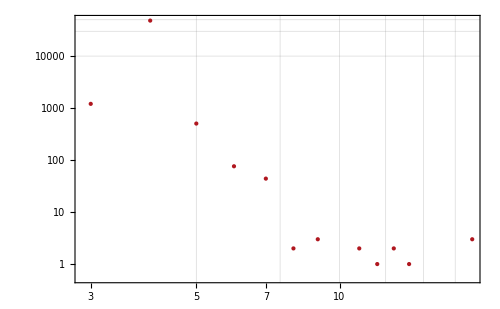

```mathematica
HistogramPointPlot[relaxationTimes,ScalingFunctions->{"Log","Log"}]
```